```mathematica
x
```

x

```mathematica
x+x
```

2 x

```mathematica
%
```

2 x

```mathematica
(*comment*)
```

```mathematica
(* min z=4x1-3x2+5
 x1+4x2<=40
-2x1+2x2>=12
-3x1- x2<=15 *)
```

```mathematica
g1[x1_,x2_]:=x1+4x2;b1=40;
g2[x1_,x2_]:=-2x1+2x2;b2=12;
g3[x1_,x2_]:=-3x1-x2;b3=15;
```

```mathematica
g1[2,3]
```

14

```mathematica
Solve[g1[x1,x2]==b1,{x2}]
```

{{x2→(40-x1)/4}}

```mathematica
Solve[g1[x1,x2]==b1,{x2}][[1,1]]
```

x2→(40-x1)/4

```mathematica
x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]]
```

(40-x1)/4

```mathematica
g1[x1_]=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]]
```

(40-x1)/4

```mathematica
g1[2]
```

19/2

```mathematica
g1[x1]
```

(40-x1)/4

```mathematica
g1[x1_]=x2/.Solve[g1[x1,x2]==b1,{x2}][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2,{x2}][[1,1]];
g3[x1_]=x2/.Solve[g3[x1,x2]==b3,{x2}][[1,1]];
```

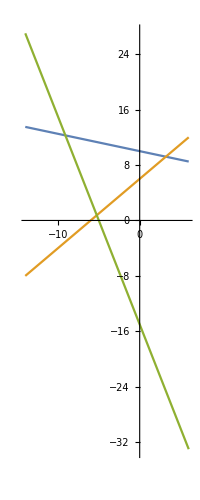

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-14,6},AspectRatio->Automatic]
```

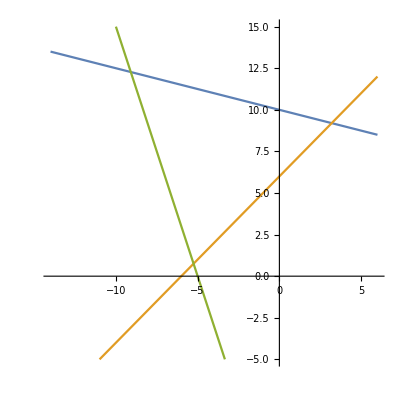

```mathematica
Plot[{g1[x],g2[x],g3[x]},{x,-14,6},AspectRatio->1,PlotRange->{-5,15}]
```

```mathematica
u={a,b,c};
v={1,2,3};
u.v
```

a+2 b+3 c

```mathematica
w={u,v,2u}
```

{{a,b,c},{1,2,3},{2 a,2 b,2 c}}

```mathematica
MatrixForm[w]
```

(a | b | c
1 | 2 | 3
2 a | 2 b | 2 c)

```mathematica
v
v.w
MatrixForm[w.v]
```

{1,2,3}

{2+7 a,4+7 b,6+7 c}

(a+2 b+3 c
14
2 a+4 b+6 c)

```mathematica
a0={u1,u2,u3,u4,s1,s2,s3,z,rhs};
a1={1,-1,4,-4,1,0,0,0,40};
a2={2,-2,-2,2,0,1,0,0,-12};
a3={-3,3,-1,1,0,0,1,0,15};
aobj={-4,4,3,-3,0,0,0,1,5};
a={a0,a1,a2,a3,aobj};
Print["a = ", MatrixForm[a]]
```

a = (u1 | u2 | u3 | u4 | s1 | s2 | s3 | z | rhs
1 | -1 | 4 | -4 | 1 | 0 | 0 | 0 | 40
2 | -2 | -2 | 2 | 0 | 1 | 0 | 0 | -12
-3 | 3 | -1 | 1 | 0 | 0 | 1 | 0 | 15
-4 | 4 | 3 | -3 | 0 | 0 | 0 | 1 | 5)

```mathematica
b0=a0;
b1=a1/4;
b2=a2+2b1;
b3=a3+b1;
bobj=aobj-3b1;
b={b0,b1,b2,b3,bobj};
Print["b = ", MatrixForm[b]]
```

b = (u1 | u2 | u3 | u4 | s1 | s2 | s3 | z | rhs
1/4 | -1/4 | 1 | -1 | 1/4 | 0 | 0 | 0 | 10
5/2 | -5/2 | 0 | 0 | 1/2 | 1 | 0 | 0 | 8
-11/4 | 11/4 | 0 | 0 | 1/4 | 0 | 1 | 0 | 25
-19/4 | 19/4 | 0 | 0 | -3/4 | 0 | 0 | 1 | -25)